# Wolfram/Chess

Wolfram Language paclet for computational analysis of chess games

## Paclet Manifest

"Documentation"

"English"

"Guides"

"Chess.nb"DocumentationEnglishGuidesChess.nb

"ReferencePages"

"Formats"

"FEN.nb"DocumentationEnglishReferencePagesFormatsFEN.nb

"PGN.nb"DocumentationEnglishReferencePagesFormatsPGN.nb

"Symbols"

"Chessboard.nb"DocumentationEnglishReferencePagesSymbolsChessboard.nb

"ChessboardQ.nb"DocumentationEnglishReferencePagesSymbolsChessboardQ.nb

"ChessboardRecognize.nb"DocumentationEnglishReferencePagesSymbolsChessboardRecognize.nb

"ChessGame.nb"DocumentationEnglishReferencePagesSymbolsChessGame.nb

"ChessGameQ.nb"DocumentationEnglishReferencePagesSymbolsChessGameQ.nb

"ChessPlayer.nb"DocumentationEnglishReferencePagesSymbolsChessPlayer.nb

"ChessViewer.nb"DocumentationEnglishReferencePagesSymbolsChessViewer.nb

"EngineEvaluate.nb"DocumentationEnglishReferencePagesSymbolsEngineEvaluate.nb

"Engine.nb"DocumentationEnglishReferencePagesSymbolsEngine.nb

"QuitEngine.nb"DocumentationEnglishReferencePagesSymbolsQuitEngine.nb

"RandomChessboard.nb"DocumentationEnglishReferencePagesSymbolsRandomChessboard.nb

"RandomChessGame.nb"DocumentationEnglishReferencePagesSymbolsRandomChessGame.nb

"StartEngine.nb"DocumentationEnglishReferencePagesSymbolsStartEngine.nb

"Tutorials"

"Kernel"

"Chessboard.wl"KernelChessboard.wl

"ChessGame.wl"KernelChessGame.wl

"ChessPlayer.wl"KernelChessPlayer.wl

"Chess.wl"KernelChess.wl

"Common.wl"KernelCommon.wl

"Engine.wl"KernelEngine.wl

"ImportExport"

"FEN.wl"KernelImportExportFEN.wl

"PGN.wl"KernelImportExportPGN.wl

"Utilities.wl"KernelImportExportUtilities.wl

"MLE"

"ChessBoard.wl"KernelMLEChessBoard.wl

"PGNFile.wl"KernelMLEPGNFile.wl

"RecordedGame.wl"KernelMLERecordedGame.wl

"Openings.wl"KernelOpenings.wl

"Pieces.wl"KernelPieces.wl

"Recognition.wl"KernelRecognition.wl

"Viewer.wl"KernelViewer.wl

"LibraryResources"

"LibraryLinkUtilities.wl"LibraryResourcesLibraryLinkUtilities.wl

"Linux-ARM64"

"ChessTools.so"LibraryResourcesLinux-ARM64ChessTools.so

"engine"LibraryResourcesLinux-ARM64engine

"Linux-x86-64"

"ChessTools.so"LibraryResourcesLinux-x86-64ChessTools.so

"engine"LibraryResourcesLinux-x86-64engine

"MacOSX-ARM64"

"ChessTools.dylib"LibraryResourcesMacOSX-ARM64ChessTools.dylib

"engine"LibraryResourcesMacOSX-ARM64engine

"MacOSX-x86-64"

"ChessTools.dylib"LibraryResourcesMacOSX-x86-64ChessTools.dylib

"engine"LibraryResourcesMacOSX-x86-64engine

"Windows-x86-64"

"ChessTools.dll"LibraryResourcesWindows-x86-64ChessTools.dll

"engine.exe"LibraryResourcesWindows-x86-64engine.exe

"LICENSE"LICENSE

"NOTICE"NOTICE

"PacletInfo.wl"PacletInfo.wl

"ResourceDefinition.nb"ResourceDefinition.nb

"Resources"

"BoxIcon.wxf"ResourcesBoxIcon.wxf

"ChessboardRecognition"

"chessboard_squares.wlnet"ResourcesChessboardRecognitionchessboard_squares.wlnet

"chess_pieces_2D.wlnet"ResourcesChessboardRecognitionchess_pieces_2D.wlnet

"lattice_points.wlnet"ResourcesChessboardRecognitionlattice_points.wlnet

"Engine"

"net.nnue"ResourcesEnginenet.nnue

"Icons.wxf"ResourcesIcons.wxf

"OpeningDatabase.wxf"ResourcesOpeningDatabase.wxf

## Web Content

### Headline Image

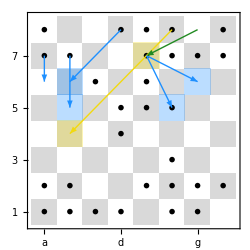

### Basic Description

Wolfram/Chess provides Import and Export capabilities for FEN and PGN formats. It allows you to import chess games and positions into Wolfram Language expressions and analyze them using the full potential of the Wolfram Language.

### Details

Additional information about the paclet.

### Primary Context

Wolfram`Chess`

### Main Guide Page

## Examples

### Initialization for Examples

```mathematica
Needs["Wolfram`Chess`"];
```

### Basic Examples

Create a symbolic representation of a chess position:

```mathematica
board=Chessboard[]
```

Chessboard[…]

Find the best move in a position given by a FEN string:

```mathematica
ImportString["4brk1/p5r1/1p5Q/4P3/2pPn3/2P5/PP1N3P/2B2R1K b - - 1 32",{"FEN","BestMove",1}]
```

Rxf1+

Create a symbolic representation of a chess game from list of moves and metadata:

```mathematica
g=ChessGame[<|
"Metadata"-><|"White"->"Alice","Black"->"Bob","Date"->Today,"Site"->(First@GeoNearest["City",Here])["Name"],"Event"->"Friendly Match","Round"->1|>,
"Moves"->{"e4","e5","Ke2","Ke7"},
"Result"->"1-0"|>
]
```

ChessGame[…]

Export game to a PGN file:

```mathematica
Export["game.pgn",g]
```

game.pgn

Start a chess game:

```mathematica
ChessPlayer[]
```

-Graphics-

### Scope

Import list of chess games from a sample PGN file:

```mathematica
Import["ExampleData/sample.pgn","ChessGames"]
```

{ChessGame[…],ChessGame[…]}

## Source & Additional Information

### Creator

Rafal Chojna <rafalc@wolfram.com>, Jay Warendorff <jayw@wolfram.com>

### Source Control Repository

https://github.com/UserName/MyPaclet

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

chess

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Original Source References and Attributions

Source, reference or citation

### Links

Link to other related material

### Compatibility

#### Wolfram Language Version

13.2+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

Wolfram Language system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

Wolfram Language built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

Additional information about limitations, issues, etc.